```mathematica
Bob ==  PDF[UniformDistribution[{0,1}],x]
```

Bob==(Piecewise[{{1, 0≤x≤1}, {0, True}}])

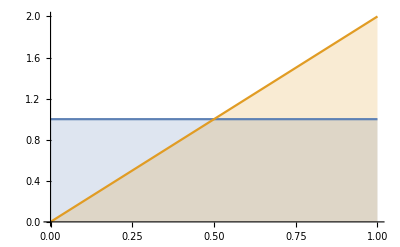

```mathematica
Plot[{PDF[UniformDistribution[{0,1}],x],2*x},{x,0,1},Filling->Axis]
```

```mathematica
g:= PDF[UniformDistribution[{0,1}],x];
f :=   (x*g)/Integrate[x*g ,{x,0,1}];
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.0000204286, 0, 1}.

NIntegrate::itraw: Raw object 0.0000204286 cannot be used as an iterator.

Integrate::ilim: Invalid integration variable or limit(s) in {0.0204286, 0, 1}.

NIntegrate::itraw: Raw object 0.0204286 cannot be used as an iterator.

General::stop: Further output of NIntegrate :: itraw will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {0.0408368, 0, 1}.

General::stop: Further output of Integrate :: ilim will be suppressed during this calculation.

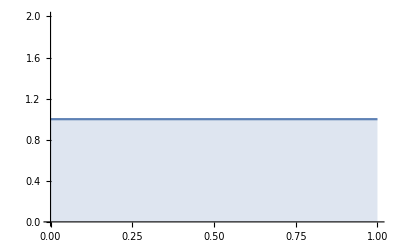

```mathematica
Plot[{g,f},{x,0,1},Filling->Axis]
```